```mathematica
c=Import["/home/johann/Documents/Projects/hobby/Function_optimization/mydata.dat","Table",HeaderLines->1];
c=c[[Length[c],;;Length[c[[1]]]-1]]
```

{2.0072,0.662551,-1.46672,0.707557,0.956734}

```mathematica
besselK1[x_]:=Exp[-x]*(1+1/x)/(c[[2]]*x^(c[[1]]/5)+c[[3]]*x^(c[[1]]/4)+c[[4]]*x^(c[[1]]/3)+c[[5]]*x^(c[[1]]/2)+(2*x/Pi)^c[[1]]+1)^(1/(2*c[[1]]));
b1[x_]:=BesselK[1,x];
```

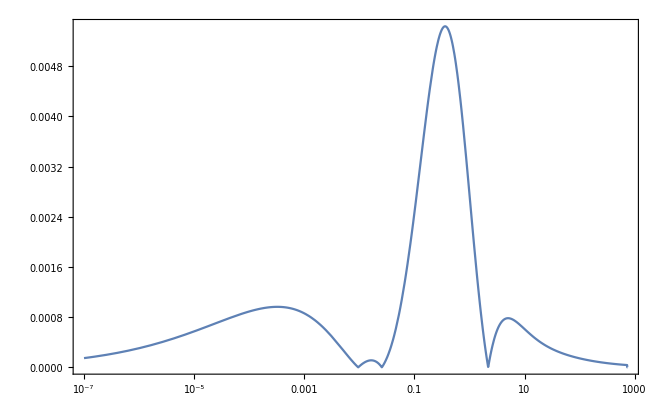

```mathematica
LogLinearPlot[{Abs[besselK1[x]/BesselK[1,x]-1]},{x,10^-7,1000},PlotTheme->"FrameGrid",PlotRange->All]
```

```mathematica
D[Exp[-x]*(1+1/x)/(c1*x^(c0/5)+c2*x^(c0/4)+c3*x^(c0/3)+c4*x^(c0/2)+(2*x/Pi)^c0+1)^(1/(2*c0)),c0]//FullSimplify
D[Exp[-x]*(1+1/x)/(c1*x^(c0/5)+c2*x^(c0/4)+c3*x^(c0/3)+c4*x^(c0/2)+(2*x/Pi)^c0+1)^(1/(2*c0)),c1]
D[Exp[-x]*(1+1/x)/(c1*x^(c0/5)+c2*x^(c0/4)+c3*x^(c0/3)+c4*x^(c0/2)+(2*x/Pi)^c0+1)^(1/(2*c0)),c2]
D[Exp[-x]*(1+1/x)/(c1*x^(c0/5)+c2*x^(c0/4)+c3*x^(c0/3)+c4*x^(c0/2)+(2*x/Pi)^c0+1)^(1/(2*c0)),c3]
D[Exp[-x]*(1+1/x)/(c1*x^(c0/5)+c2*x^(c0/4)+c3*x^(c0/3)+c4*x^(c0/2)+(2*x/Pi)^c0+1)^(1/(2*c0)),c4]
```

1/(2 c0^2)ⅇ^-x (1+1/x) (1+c1 x^(c0/5)+c2 x^(c0/4)+c3 x^(c0/3)+c4 x^(c0/2)+(2/π)^c0 x^c0)^(-1/2/c0) (-(c0 ((12 c1 x^(c0/5)+15 c2 x^(c0/4)+20 c3 x^(c0/3)+30 c4 x^(c0/2)) Log[x]+15 2^(2+c0) π^-c0 x^c0 Log[(2 x)/π]))/(60 (1+c1 x^(c0/5)+c2 x^(c0/4)+c3 x^(c0/3)+c4 x^(c0/2)+(2/π)^c0 x^c0))+Log[1+c1 x^(c0/5)+c2 x^(c0/4)+c3 x^(c0/3)+c4 x^(c0/2)+(2/π)^c0 x^c0])

-(ⅇ^-x (1+1/x) x^(c0/5) (1+c1 x^(c0/5)+c2 x^(c0/4)+c3 x^(c0/3)+c4 x^(c0/2)+(2/π)^c0 x^c0)^(-1-1/(2 c0)))/(2 c0)

-(ⅇ^-x (1+1/x) x^(c0/4) (1+c1 x^(c0/5)+c2 x^(c0/4)+c3 x^(c0/3)+c4 x^(c0/2)+(2/π)^c0 x^c0)^(-1-1/(2 c0)))/(2 c0)

-(ⅇ^-x (1+1/x) x^(c0/3) (1+c1 x^(c0/5)+c2 x^(c0/4)+c3 x^(c0/3)+c4 x^(c0/2)+(2/π)^c0 x^c0)^(-1-1/(2 c0)))/(2 c0)

-(ⅇ^-x (1+1/x) x^(c0/2) (1+c1 x^(c0/5)+c2 x^(c0/4)+c3 x^(c0/3)+c4 x^(c0/2)+(2/π)^c0 x^c0)^(-1-1/(2 c0)))/(2 c0)

```mathematica
D[Abs[a*x^2/f(x)-1],a]
```

(x^3 Abs'[-1+(a x^3)/f])/f